```mathematica
N-sf-N-I-S junction for YSR states ,without Andreev approximation
```

## Spin up incident electron

```mathematica
Clear["Global`*"]


S= 1/2;
m1= -1/2;
Δ= 1.;
Ef= 50;
F= 1.;
kfa=  0.85*π;J=4.5;
(*listbs=ParallelTable[*)
ke1=kh1=1;qp1=qm1=1;
SetSharedVariable[listbs10]
listbs10={};
ParallelDo[{

a1=1;
a2=0;
a3=0;
a4=0;
a5=-1;
a6=0;
a7=-Exp[I*kfa*ke1];
a8=0;
a9=0;
a10=0;
a11=0;
a12=0;
a13=0;
a14=0;
a15=0;
a16=0;
z1=-1;


b1=0;
b2=1;
b3=0;
b4=0;
b5=0;
b6=-1;
b7=0;
b8=-Exp[I*kfa*ke1];
b9=0;
b10=0;
b11=0;
b12=0;
b13=0;
b14=0;
b15=0;
b16=0;
z2=0;


c1=0;
c2=0;
c3=1;
c4=0;
c5=0;
c6=0;
c7=0;
c8=0;
c9=-Exp[-I*kfa*kh1];
c10=0;
c11=-1; 
c12=0; 
c13=0;
c14=0;
c15=0;
c16=0;
z3=0;


d1=0;
d2=0;
d3=0;
d4=1;
d5=0;
d6=0;
d7=0;
d8=0;
d9=0;
d10=-Exp[-I*kfa*kh1]; 
d11=0;
d12=-1;
d13=0;
d14=0;
d15=0;
d16=0;
z4=0;


e1=ke1-I*J*m1;
e2=-I*J*F;
e3=0;
e4=0;
e5=ke1;
e6=0;
e7=-ke1*Exp[I*kfa*ke1];
e8=0;
e9=0;
e10=0;
e11=0;
e12=0;
e13=0;
e14=0;
e15=0;
e16=0;
z5=ke1+I*J*m1;


f1=-I*J*F;
f2=ke1+I*J*(m1+1);
f3=0;
f4=0;
f5=0;
f6=ke1;
f7=0;
f8=-ke1*Exp[I*kfa*ke1];
f9=0;
f10=0;
f11=0;
f12=0;
f13=0;
f14=0;
f15=0;
f16=0;
z6=I*J*F;


g1=0;
g2=0;
g3=-kh1+I*J*(m1+1); (* - I*)
g4=-I*J*F;
g5=0;
g6=0;
g7=0;
g8=0;
g9=kh1*Exp[-I*kfa*kh1];
g10=0;
g11=-kh1;
g12=0;
g13=0;
g14=0;
g15=0;
g16=0;
z7=0;


h1=0;
h2=0;
h3=-I*J*F;
h4=-kh1-I*J*(m1);
h5=0;
h6=0;
h7=0;
h8=0;
h9=0;
h10=kh1*Exp[-I*kfa*kh1];
h11=0;
h12=-kh1;
h13=0;
h14=0;
h15=0;
h16=0;
z8=0;


i1=0;
i2=0;
i3=0;
i4=0;
i5=Exp[I*kfa*ke1]; 
i6=0;  
i7=1;
i8=0;
i9=0;
i10=0;
i11=0;
i12=0;
i13=-u*Exp[I*kfa*qp1]; 
i14=0;
i15=0;
i16=-v*Exp[-I*kfa*qm1]; 
z9=0;


j1=0;
j2=0;
j3=0;
j4=0;
j5=0;
j6=Exp[I*kfa*ke1];
j7=0;
j8=1;
j9=0;      
j10=0;
j11=0;
j12=0;
j13=0;
j14=-u*Exp[I*kfa*qp1];  
j15=v*Exp[-I*kfa*qm1];    
j16=0;
z10=0;


t1=0;
t2=0;
t3=0;
t4=0;
t5=0;
t6=0;
t7=0;
t8=0;
t9=1;
t10=0;
t11=Exp[-I*kfa*kh1]; 
t12=0;
t13=0;
t14=v*Exp[I*kfa*qp1];
t15=-u*Exp[-I*kfa*qm1];  
t16=0;      
z11=0;


l1=0;
l2=0;
l3=0;
l4=0;
l5=0;
l6=0;
l7=0;  
l8=0;
l9=0;
l10=1;
l11=0;
l12=Exp[-I*kfa*kh1];
l13=-v*Exp[I*kfa*qp1];
l14=0; 
l15=0;  
l16=-u*Exp[-I*kfa*qm1];
z12=0;


p1=0;
p2=0;
p3=0;
p4=0;
p5=-(ke1-I*2*Z)*Exp[I*kfa*ke1];                
p6=0; 
p7=(ke1+I*2*Z);
p8=0;
p9=0;
p10=0;
p11=0;
p12=0;
p13=u*qp1*Exp[I*kfa*qp1]; 
p14=0;
p15=0;
p16=-v*qm1*Exp[-I*kfa*qm1];
z13=0;


q1=0;
q2=0;
q3=0;
q4=0;
q5=0;
q6=-(ke1-I*2*Z)*Exp[I*kfa*ke1];
q7=0;
q8=(ke1+I*2*Z);   
q9=0;
q10=0;
q11=0;
q12=0;
q13=0;
q14=u*qp1*Exp[I*kfa*qp1];
q15=v*qm1*Exp[-I*kfa*qm1];
q16=0;
z14=0;


r1=0;
r2=0;
r3=0;
r4=0;
r5=0;
r6=0;
r7=0;
r8=0;
r9=-(kh1-I*2*Z);
r10=0;   
r11=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
r12=0;
r13=0;
r14=-v*qp1*Exp[I*kfa*qp1];
r15=-u*qm1*Exp[-I*kfa*qm1];
r16=0; 
z15=0;


w1=0;
w2=0;
w3=0;
w4=0;
w5=0;
w6=0;
w7=0;   
w8=0;
w9=0;
w10=-(kh1-I*2*Z);
w11=0;
w12=(kh1+I*2*Z)*Exp[-I*kfa*kh1];
w13=v*qp1*Exp[I*kfa*qp1];
w14=0;  
w15=0;  
w16=-u*qm1*Exp[-I*kfa*qm1];
z16=0;


A={{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16},{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16},{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16},{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12,d13,d14,d15,d16},{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16},{g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15,g16},{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,h11,h12,h13,h14,h15,h16},{i1,i2,i3,i4,i5,i6,i7,i8,i9,i10,i11,i12,i13,i14,i15,i16 },{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14 ,j15 ,j16},{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14 ,t15 ,t16},{l1,l2,l3,l4,l5,l6,l7,l8,l9,l10,l11,l12,l13 ,l14,l15,l16 },{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13 ,p14,p15,p16 },{q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14 ,q15 ,q16},{r1,r2,r3,r4,r5,r6,r7,r8,r9,r10,r11,r12,r13,r14 ,r15 ,r16},{w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,w11,w12,w13 ,w14,w15,w16 }}; 

B={z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16};

Sol=Refine[LinearSolve[A,B],Element[Ed,Reals]]; 


b1s=Sol[[1]]/.{u-> (1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),v-> (1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2) }; 
bc=Chop[b1s,10^-5];
sc0=ComplexExpand[Abs[bc]^2]/.{Arg[1-Ed^2]-> 0,Arg[-1+1/Ed^2]-> 0};
scc0=Chop[sc0,10^-5];
sct0=Together[scc0];
sd10=Denominator[sct0];
sd11=Simplify[sd10,{-1<Ed<1}];
bous0=Re[Ed]/.NSolve[sd11== 0,{Ed}][[2]];
listbs0=AppendTo[listbs10,{Z,Abs[bous0],-Abs[bous0]}]},{Z,0.001,2.2,0.04}];//AbsoluteTiming
listbs0=Sort[listbs10]

(*Ss=Sol[[1]];
st=Together[Ss];
       sd=Denominator[st];
Sc=ComplexExpand[Abs[sd]^2];
bous=Ed/.FindRoot[Sc== 0,{Ed,0}];
{Z,Re[bous]},{Z,0.001,2.2,0.1}];
listbs=SortBy[listbs,First];*)
```

{35.2576,Null}

{{0.001,0.885799,-0.885799},{0.041,0.868581,-0.868581},{0.081,0.848311,-0.848311},{0.121,0.82443,-0.82443},{0.161,0.796317,-0.796317},{0.201,0.763319,-0.763319},{0.241,0.724811,-0.724811},{0.281,0.680305,-0.680305},{0.321,0.629597,-0.629597},{0.361,0.572937,-0.572937},{0.401,0.511165,-0.511165},{0.441,0.445743,-0.445743},{0.481,0.378631,-0.378631},{0.521,0.312025,-0.312025},{0.561,0.248026,-0.248026},{0.601,0.18839,-0.18839},{0.641,0.134387,-0.134387},{0.681,0.0868001,-0.0868001},{0.721,0.0460175,-0.0460175},{0.761,0.0121439,-0.0121439},{0.801,0.0148847,-0.0148847},{0.841,0.0352118,-0.0352118},{0.881,0.0489982,-0.0489982},{0.921,0.0563815,-0.0563815},{0.961,0.0574534,-0.0574534},{1.001,0.0522508,-0.0522508},{1.041,0.0407559,-0.0407559},{1.081,0.0229077,-0.0229077},{1.121,0.,0.},{1.161,0.0321692,-0.0321692},{1.201,0.0694776,-0.0694776},{1.241,0.113182,-0.113182},{1.281,0.162951,-0.162951},{1.321,0.21816,-0.21816},{1.361,0.27782,-0.27782},{1.401,0.340564,-0.340564},{1.441,0.404713,-0.404713},{1.481,0.468424,-0.468424},{1.521,0.529915,-0.529915},{1.561,0.58768,-0.58768},{1.601,0.640647,-0.640647},{1.641,0.688223,-0.688223},{1.681,0.730254,-0.730254},{1.721,0.766919,-0.766919},{1.761,0.798614,-0.798614},{1.801,0.825844,-0.825844},{1.841,0.849153,-0.849153},{1.881,0.869067,-0.869067},{1.921,0.886073,-0.886073},{1.961,0.900604,-0.900604},{2.001,0.995601,-0.995601},{2.041,0.92369,-0.92369},{2.081,0.932842,-0.932842},{2.121,0.940723,-0.940723},{2.161,0.947527,-0.947527}}

{{0.001,0.665948,-0.665948},{0.041,0.663065,-0.663065},{0.081,0.676146,-0.676146},{0.121,0.700155,-0.700155},{0.161,0.730947,-0.730947},{0.201,0.76502,-0.76502},{0.241,0.799484,-0.799484},{0.281,0.832144,-0.832144},{0.321,0.861567,-0.861567},{0.361,0.887039,-0.887039},{0.401,0.908426,-0.908426},{0.441,0.925989,-0.925989},{0.481,0.940197,-0.940197},{0.521,0.951585,-0.951585},{0.561,0.960673,-0.960673},{0.601,0.967919,-0.967919},{0.641,0.973706,-0.973706},{0.681,0.978343,-0.978343},{0.721,0.982074,-0.982074},{0.761,0.985091,-0.985091},{0.801,0.987542,-0.987542},{0.841,0.989545,-0.989545},{0.881,0.991188,-0.991188},{0.921,0.992544,-0.992544},{0.961,0.993668,-0.993668},{1.001,0.994603,-0.994603},{1.041,0.995384,-0.995384},{1.081,0.99604,-0.99604},{1.121,0.996592,-0.996592},{1.161,0.997059,-0.997059},{1.201,0.997455,-0.997455},{1.241,1.03149,-1.03149},{1.281,1.02825,-1.02825},{1.321,0.998242,-0.998242},{1.361,1.02288,-1.02288},{1.401,0.972141,-0.972141},{1.441,0.99883,-0.99883},{1.481,0.998973,-0.998973},{1.521,1.01165,-1.01165},{1.561,0.999205,-0.999205},{1.601,1.00036,-1.00036},{1.641,1.0003,-1.0003},{1.681,0.999451,-0.999451},{1.721,0.999513,-0.999513},{1.761,0.999567,-0.999567},{1.801,0.999615,-0.999615},{1.841,0.999657,-0.999657},{1.881,1.00011,-1.00011},{1.921,1.0001,-1.0001},{1.961,0.999756,-0.999756},{2.001,0.999781,-0.999781},{2.041,0.999804,-0.999804},{2.081,0.999824,-0.999824},{2.121,1.00005,-1.00005},{2.161,0.999858,-0.999858}}

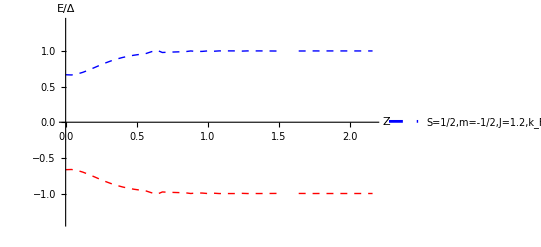

```mathematica
ListLinePlot[{listbs0[[All,{1,2}]],listbs0[[All,{1,3}]]},PlotRange->{-1.4,1.4},PlotStyle->{{Blue,Dashed,Thick},{Red,Dashed,Thick},{Black,Dashed,Thick}},AxesLabel-> {"Z","E/Δ"},PlotLegends->Placed[{"S=1/2,m=-1/2,J=1.2,k_Fa=0.5π"},{Right,Top}],LabelStyle->{FontSize->18}]
```

```mathematica
(*bous0=Re[Ed]/.NSolve[sd11== 0,{Ed}][[2]];
listbs0=AppendTo[listbs10,{Z,bous0,-bous0}]},{Z,0.001,2.2,0.05}];//AbsoluteTiming*)
```

{28.9504,Null}

{{0.001,-0.885799,0.885799},{0.051,-0.86382,0.86382},{0.101,-0.836859,0.836859},{0.151,-0.803778,0.803778},{0.201,-0.763319,0.763319},{0.251,-0.71426,0.71426},{0.301,-0.655723,0.655723},{0.351,-0.587625,0.587625},{0.401,-0.511165,0.511165},{0.451,-0.429039,0.429039},{0.501,-0.345128,0.345128},{0.551,-0.263678,0.263678},{0.601,-0.18839,0.18839},{0.651,-0.121867,0.121867},{0.701,-0.0655466,0.0655466},{0.751,-0.0199661,0.0199661},{0.801,-0.0148847,0.0148847},{0.851,-0.0392656,0.0392656},{0.901,-0.0534832,0.0534832},{0.951,-0.0577742,0.0577742},{1.001,-0.0522508,0.0522508},{1.051,-0.0368926,0.0368926},{1.101,-0.0115752,0.0115752},{1.151,-0.023859,0.023859},{1.201,-0.0694776,0.0694776},{1.251,-0.125074,0.125074},{1.301,-0.189928,0.189928},{1.351,-0.262556,0.262556},{1.401,-0.340564,0.340564},{1.451,-0.420754,0.420754},{1.501,-0.499549,0.499549},{1.551,-0.573655,0.573655},{1.601,-0.640647,0.640647},{1.651,-0.699248,0.699248},{1.701,-0.749236,0.749236},{1.751,-0.791129,0.791129},{1.801,-0.825844,0.825844},{1.851,-0.85443,0.85443},{1.901,-0.877905,0.877905},{1.951,-0.897182,0.897182},{2.001,-0.913035,0.913035},{2.051,-0.926109,0.926109},{2.101,-0.936929,0.936929},{2.151,-0.945918,0.945918}}

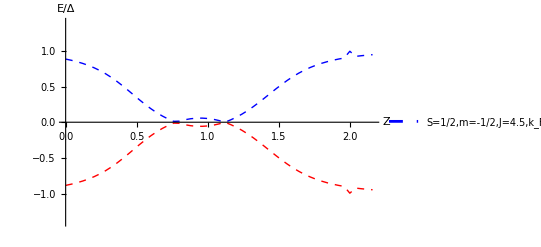

```mathematica
ListLinePlot[{listbs0[[All,{1,2}]],listbs0[[All,{1,3}]]},PlotRange->{-1.4,1.4},PlotStyle->{{Blue,Dashed,Thick},{Red,Dashed,Thick},{Black,Dashed,Thick}},AxesLabel-> {"Z","E/Δ"},PlotLegends->Placed[{"S=1/2,m=-1/2,J=4.5,k_Fa=0.85π"},{Right,Top}],LabelStyle->{FontSize->18}]
```

```mathematica
u=(1/2*(1+I((-Ed^2+Δ^2)/Ed^2)^(1/2)))^(1/2); (*(1/2*(1+(I(-Ed^2+Δ^2)^(1/2))/Abs[Ed]))^(1/2); *)
v=(1/2*(1-I((-Ed^2+Δ^2)/Ed^2)^(1/2)))^(1/2) ;(*(1/2*(1-((Ed^2-Δ^2)^(1/2))/Abs[Ed]))^(1/2)*)
(*ke1=√(1+Ed/Ef); kh1=√(1-Ed/Ef);
qp1=√(1+(I(-Ed^2+Δ^2)^(1/2))/Ef);(*Piecewise[{{√(1+((Ed^2-Δ^2)^(1/2))/Ef),Abs[Ed]>Δ},{√(1+(I(-Ed^2+Δ^2)^(1/2))/Ef),Abs[Ed]<Δ}}];*)
qm1=√(1-(I(-Ed^2+Δ^2)^(1/2))/Ef); (*Piecewise[{{√(1-((Ed^2-Δ^2)^(1/2))/Ef),Abs[Ed]>Δ},{√(1-(I(-Ed^2+Δ^2)^(1/2))/Ef),Abs[Ed]<Δ}}];*)*)
```